```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
files1=FileNames["TYPES_N1000_g500_runs1_pswitch0.0000_pintro0.0*_Tmut*_types5_*.txt"];
Data1=Table[Import[files1[[f]],"Table"],{f,1,Length[files1]}];

files2=FileNames["TYPES_N1000_g600_runs*_pswitch0.0000_pintro0.0*_Tmut*_types10_*.txt"];
Data2=Table[Import[files2[[f]],"Table"],{f,1,Length[files2]}];

files3=FileNames["TYPES_N1000_g600_runs*_pswitch0.0000_pintro0.0*_Tmut*_types20_*.txt"];
Data3=Table[Import[files3[[f]],"Table"],{f,1,Length[files3]}];

files4=FileNames["TYPES_N1000_g600_runs*_pswitch0.0000_pintro0.0*_Tmut*_types50_*.txt"];
Data4=Table[Import[files4[[f]],"Table"],{f,1,Length[files4]}];

files5=FileNames["TYPES_N1000_g500_runs*_pswitch0.0000_pintro0.0*_Tmut*_types100_*.txt"];
Data5=Table[Import[files5[[f]],"Table"],{f,1,Length[files5]}];
```

```mathematica
ratios1 = Table[Table[Min[Data1[[j]][[i]]]/Max[Data1[[j]][[i]]], {i,1, 450}],{j,1,Dimensions[Data1][[1]]}]*1.0;
ratios2 = Table[Table[Min[Data2[[j]][[i]]]/Max[Data2[[j]][[i]]], {i,1, 450}],{j,1,Dimensions[Data2][[1]]}]*1.0;
ratios3 = Table[Table[Min[Data3[[j]][[i]]]/Max[Data3[[j]][[i]]], {i,1, 450}],{j,1,Dimensions[Data3][[1]]}]*1.0;
ratios4 =Table[Table[Min[Data4[[j]][[i]]]/Max[Data4[[j]][[i]]], {i,1, 450}],{j,1,Dimensions[Data4][[1]]}]*1.0;
ratios5 = Table[Table[Min[Data5[[j]][[i]]]/Max[Data5[[j]][[i]]], {i,1, 450}],{j,1,Dimensions[Data5][[1]]}]*1.0;
```

```mathematica
meanRatios1 = Mean[ratios1];
meanRatios2 = Mean[ratios2];
meanRatios3 = Mean[ratios3];
meanRatios4 = Mean[ratios4];
meanRatios5 = Mean[ratios5];
```

```mathematica
.
```

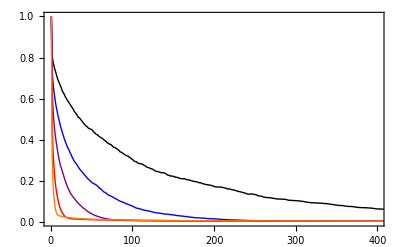

```mathematica
Show[ListLinePlot[{meanRatios1, meanRatios2, meanRatios3, meanRatios4,meanRatios5}, PlotRange->{{0,400},{0,1}}, PlotStyle->{{Black,Thick},{Blue,Thick},{Purple,Thick},{Red,Thick},{Orange,Thick}}], Frame->True,FrameTicksStyle->Directive[16, Black, FontFamily->"Times"]]
```

```mathematica
test=Table[Table[Dimensions[Data5][[3]]-Length[Flatten[Position[Data5[[j]][[i]]-1,0]]], {i,1,500}],{j,1,500}];
typesLeft100=Mean[test]*1.0;

test=Table[Table[Dimensions[Data4][[3]]-Length[Flatten[Position[Data4[[j]][[i]]-1,0]]], {i,1,500}],{j,1,500}];
typesLeft50=Mean[test]*1.0;

test=Table[Table[Dimensions[Data3][[3]]-Length[Flatten[Position[Data3[[j]][[i]]-1,0]]], {i,1,500}],{j,1,500}];
typesLeft20=Mean[test]*1.0;

test=Table[Table[Dimensions[Data2][[3]]-Length[Flatten[Position[Data2[[j]][[i]]-1,0]]], {i,1,500}],{j,1,500}];
typesLeft10=Mean[test]*1.0;

test=Table[Table[Dimensions[Data1][[3]]-Length[Flatten[Position[Data1[[j]][[i]]-1,0]]], {i,1,500}],{j,1,500}];
typesLeft5=Mean[test]*1.0;
```

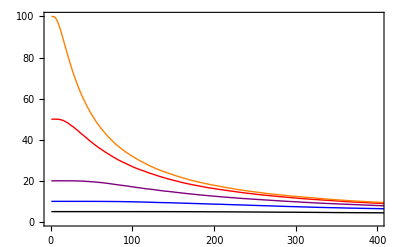

```mathematica
Show[ListLinePlot[{typesLeft5,typesLeft10,typesLeft20, typesLeft50,typesLeft100}, PlotRange->{{0,400},{0,100}}, PlotStyle->{{Black,Thick},{Blue,Thick},{Purple,Thick},{Red,Thick},{Orange,Thick}}], Frame->True,FrameTicksStyle->Directive[16, Black, FontFamily->"Times"]]
```

```mathematica
files5=FileNames["TYPES_N1000_g500_runs*_pswitch0.0000_pintro0.0*_Tmut*_types100_*.txt"];
Data5=Table[Import[files5[[f]],"Table"],{f,1,Length[files5]}];
```